```mathematica
ClearAll[r2,x,y,up,vp, x,x0,y, y0,η ,λ,γ,ρ];
r2[x_,y_,x0_,y0_]=(x-x0)^2+(y-y0)^2;
up[x_,y_,x0_,y0_]=-λ/(2 π) (y-y0) Exp[η (1- r2[x,y,x0,y0])];
vp[x_,y_,x0_,y0_]=λ/(2 π) (x-x0) Exp[η (1- r2[x,y,x0,y0])];
u0=1;
v0=1;
vel[x_,y_,x0_,y0_]=Sqrt[(u0+up[x,y,x0,y0])^2+(v0+vp[x,y,x0,y0])^2];
velp[x_,y_,x0_,y0_]=Sqrt[(up[x,y,x0,y0])^2+(vp[x,y,x0,y0])^2];
vel0[x_,y_]=Sqrt[(u0)^2+(v0)^2];
ρ[x_,y_,x0_,y0_]=(1-((γ-1)λ^2)/(16 γ η π^2)Exp[2 η (1-r2[x,y,x0,y0])])^(1/(γ-1));
divergence[x_,y_,x0_,y0_]=D[ρ[x,y,x0,y0](u0+up[x,y,x0,y0]),x]+
D[ρ[x,y,x0,y0](v0+vp[x,y,x0,y0]),y];
divergence2[x_,y_,x0_,y0_]=D[(u0+up[x,y,x0,y0]),x]+
D[(v0+vp[x,y,x0,y0]),y];

velt[x_,y_,t_]=Sqrt[(u0+up[x,y,x0+t,y0+t])^2+(v0+vp[x,y,x0+t,y0+t])^2];
ρt[x_,y_,t_]=ρ[x,y,x0+t,y0+t];
```

```mathematica
γ=1.4;  (*specific heat ratio; 1.4*)
η=1; (* determines gradient of solution *)
λ=5;(* strength of vortex *)
x0=-5;
y0=-5;
ρ0[x_,y_]=1;
Δ=2.5;
```

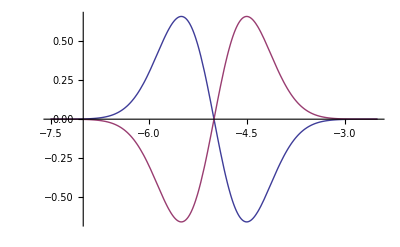

{1.69136,{x→-4.5}}

```mathematica
Plot[{up[x,x,x0,y0],vp[x,x,x0,y0]},{x,x0-Δ,x0+Δ},PlotRange->All]
NMaximize[velt[x,x,0],x]
```

```mathematica
peclet =0.5 7.326 10^-2  2.34 / (4.5 10^-2)
```

1.90476

```mathematica
ρt[-4,-4,0] velt[-4,-4,0]
```

1.45112

```mathematica
Plot3D[Sqrt[(ρt[x,y,0] )],{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ},PlotRange->All]
```

-Graphics3D-

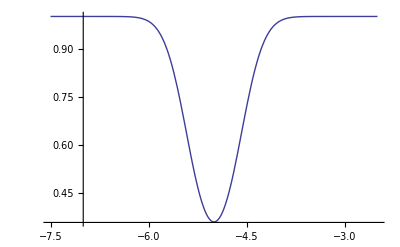

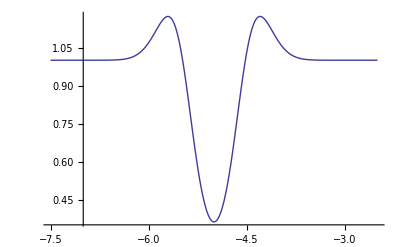

-Graphics-

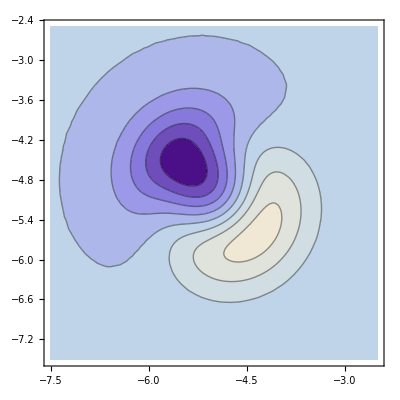

-Graphics-

```mathematica
Plot[ρt[x,x,0],{x,x0-Δ,x0+Δ},PlotRange->All]
Plot[1/2 ρ[x,x,x0,y0] vel[x,x,x0,y0]^2,{x,x0-Δ,x0+Δ},PlotRange->All]
Plot[(ρ[x,x]-1) up[x,x,x0,y0],{x,x0-Δ,x0+Δ},PlotRange->All]

ContourPlot[Sqrt[ρ[x,y,x0,y0]] vel[x,y,x0,y0],{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ},PlotRange->All]
ContourPlot[Sqrt[ρ[x,y,x0,y0]] vel[x,y,x0,y0],{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ},PlotRange->All]
```

-Graphics3D-

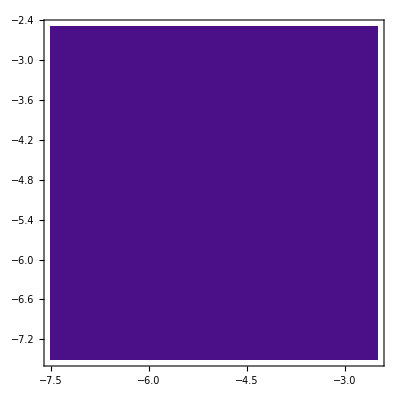

```mathematica
Plot3D[divergence2[x,y,x0,y0],{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ},PlotRange->All]
ContourPlot[divergence2[x,y,x0,y0],{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ},PlotRange->All]
```

```mathematica
(* Total kinetic energy *)
Δ=2.527;
1/2 NIntegrate[ρ[x,y,x0,y0]  (vel[x,y,x0,y0])^2,{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ}]
```

25.8836

```mathematica
(* Show that velocity field is divergence free *)
D[up[x,y],x]+D[vp[x,y],y]
```

vp^(0,1)[x,y]+up^(1,0)[x,y]

```mathematica
x0ns=0;
y0ns=0;
ke[t_]:=1/2 NIntegrate[ρt[x,y,t]  (velt[x,y,t])^2,{x,x0ns-Δ,x0ns+Δ},{y,y0ns-Δ,y0ns+Δ}]
```

```mathematica
(*Plot[ke[t],{t,0,10},PlotRange->All]*)
```

```mathematica
uns[x_,y_,x0_,y0_]=(u0+up[x,y,x0,y0] )Sqrt[ρ[x,y,x0,y0]];
vns[x_,y_,x0_,y0_]=(v0+vp[x,y,x0,y0])Sqrt[ρ[x,y,x0,y0]];
KEns[x_,y_,x0_,y0_] = 1/2(uns[x,y,x0,y0]^2+vns[x,y,x0,y0]^2);
KE[x_,y_,x0_,y0_] = ρ[x,y,x0,y0]/2((u0+up[x,y,x0,y0])^2+(v0+vp[x,y,x0,y0])^2);
Plot3D[{KEns[x,y,x0,y0]/KE[x,y,x0,y0]},{x,x0-Δ,x0+Δ},{y,y0-Δ,y0+Δ},PlotRange->All]
```

-Graphics3D-